```mathematica
taska[sub_,a_, tmax_]:= Module[{asymp,eqa},
eqa = (x''[t]+ω^2 x[t]+δ b x[t]^3 == 0)/.sub;
asymp = Evaluate[AsymptoticDSolveValue[{eqa,x[0]==a,x'[0]==0},x[t],{t,0,2}]];
Print[asymp];
Print[Plot[asymp, {t, 0, tmax}]];
Print[Plot[Evaluate[x[t]/.NDSolve[{eqa, x[0]==a,x'[0]==0}, x, {t, 0, 5}][[1]]], {t, 0,tmax}]]
]
```

1.-0.505 t^2

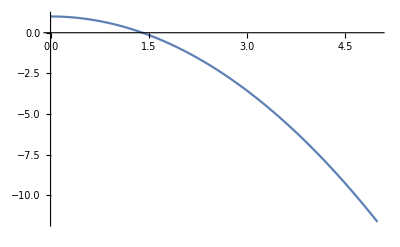

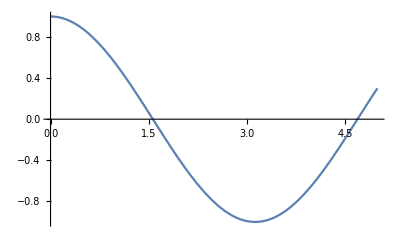

```mathematica
taska[{ω->1, δ->0.01, b->1}, 1, 5]
```

```mathematica
taskb[sub_,v0_, tmax_, deg_]:= Module[{asymp,eqa},
eqa = (x''[t]+ω^2 x[t]-δ b x[t]^3 == 0)/.sub;
asymp = Evaluate[AsymptoticDSolveValue[{eqa,x[0]==0,x'[0]==v0},x[t],{t,0,deg}]];
Print[asymp];
Print[Plot[asymp, {t, 0, tmax}]];
Print[Plot[Evaluate[x[t]/.NDSolve[{eqa, x[0]==0,x'[0]==v0}, x, {t, 0, 5}][[1]]], {t, 0,tmax}]]
]
```

t-0.166667 t^3

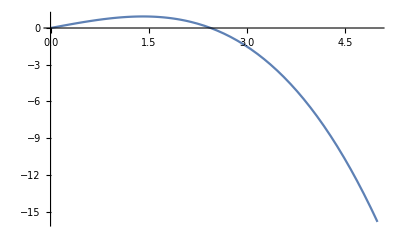

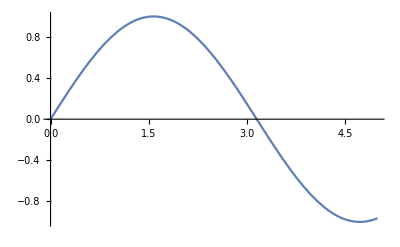

```mathematica
taskb[{ω->1, δ->0.01, b->1}, 1, 5, 4]
```

```mathematica
taskc[sub_, tmax_, deg_]:= Module[{asymp,eqa},
eqa = {t x'[t]==x+δ y[t], t y'[t]==(2 - x[t]) y[t]}/.sub;
asymp = Evaluate[AsymptoticDSolveValue[{eqa,x[0]==0,x'[0]==v0},{x[t], y[t]},{t,0,deg}]];
Print[asymp];
Print[Plot[asymp, {t, 0, tmax}]];
Print[Plot[Evaluate[x[t]/.NDSolve[{eqa, x[0]==0,x'[0]==v0}, ,{x[t], y[t]}, {t, 0, 5}][[1]]], {t, 0,tmax}]]
]
```

```mathematica
taskc[{δ->0.01}, 5, 4]
```

Set::write: Tag Times in t x'[t] is Protected.

Set::write: Tag Times in t y'[t] is Protected.

AsymptoticDSolveValue[{{x+0.01 y[t],(2-x[t]) y[t]},x[0]==0,x'[0]==v0},{x[t],y[t]},{t,0,4}]

AsymptoticDSolveValue::asvar: 0.000102143 is not a valid variable.

AsymptoticDSolveValue::aord: Approximation order specification 4. should be a positive integer.

AsymptoticDSolveValue::asvar: 0.102143 is not a valid variable.

AsymptoticDSolveValue::aord: Approximation order specification 4. should be a positive integer.

AsymptoticDSolveValue::asvar: 0.204184 is not a valid variable.

General::stop: Further output of AsymptoticDSolveValue::asvar will be suppressed during this calculation.

AsymptoticDSolveValue::aord: Approximation order specification 4. should be a positive integer.

General::stop: Further output of AsymptoticDSolveValue::aord will be suppressed during this calculation.

-Graphics-

NDSolve::deqn: Equation or list of equations expected instead of x+0.01 y[t] in the first argument {{x+0.01 y[t],(2-x[t]) y[t]},x[0]==0,x'[0]==v0}.

ReplaceAll::rmix: Elements of {{x+0.01 y[t],(2-x[t]) y[t]},x[0]==0,x'[0]==v0} are a mixture of lists and nonlists.

ReplaceAll::rmix: Elements of {{x+0.01 y[0.000102143],(2-x[0.000102143]) y[0.000102143]},x[0]==0,x'[0]==v0} are a mixture of lists and nonlists.

ReplaceAll::rmix: Elements of {{x+0.01 y[0.000102143],(2.-1. x[0.000102143]) y[0.000102143]},x[0.]==0.,x'[0.]==v0} are a mixture of lists and nonlists.

General::stop: Further output of ReplaceAll::rmix will be suppressed during this calculation.

-Graphics-

```mathematica
eqa = {t x'[t]==x[t]+δ y[t], t y'[t]==(2 - x[t]) y[t]}/.{δ->0.01}
```

{t x'[t]==x[t]+0.01 y[t],t y'[t]==(2-x[t]) y[t]}

```mathematica
Evaluate[AsymptoticDSolveValue[Join[eqa,{x[1]==1, y[1]==1/E}],{x[t], y[t]},{t,0,4}]]
```

AsymptoticDSolveValue[{t x'[t]==x[t]+0.01 y[t],t y'[t]==(2-x[t]) y[t],x[1]==1,y[1]==1/ⅇ},{x[t],y[t]},{t,0,4}]